```mathematica
relDevWOLogs[backorbit_,fx_,precision_]:=
Module[{j,k,el,z,,loglinpairs,loglinpair,la,arg,args,nm,aa,xx,b1,m1,bb,zeros,zr,approxr,estimate,fxerror,relerror,relerrors,rellog,relerrmoduli},
zeros=backorbit;
el=Length[zeros];
args={};
loglinpairs={};

k=1;
z=zeros[[k]];
la=Re[Log[Abs[z-fx]]];
arg=Arg[z-fx];
loglinpair={arg,la};
args=Append[args,arg];
loglinpairs=Append[loglinpairs,loglinpair];

For[k=1,k<el,k++;
z=zeros[[k]];
la=Re[Log[Abs[z-fx]]];
arg=Arg[z-fx];
While[Not[arg>Max[args]],arg=arg+2*Pi];
args=Append[args,arg];
loglinpair={arg,la};
loglinpairs=Append[loglinpairs,loglinpair]];

outargs=args;
outpairs=loglinpairs;
nm=FindFit[loglinpairs,aa*xx+bb,{aa,bb},{xx},PrecisionGoal->precision];
m1=nm[[1,2]];
b1=nm[[2,2]];

relerrors={};
relerrmoduli={};
j=1;
zr=zeros[[j]];
arg=args[[1]];
approxr=Exp[m1*arg+b1];
estimate=approxr*(Cos[arg]+I*Sin[arg]);
fxerror=zr-fx-estimate;
relerror=Abs[fxerror/(zr-fx)];(* denominator should be zr - fx  *)
relerrors=Append[relerrors,relerror];

For[j=1,j<Length[zeros],j++;
zr=zeros[[j]];
arg=args[[j]];
approxr=Exp[m1*arg+b1];
estimate=approxr*(Cos[arg]+I*Sin[arg]);
fxerror=zr-fx-estimate;
relerror=Abs[fxerror/(zr-fx)];
relerrors=Append[relerrors,relerror];
outerrors=relerrors;
];
Return[relerrors]]
```

```mathematica
stream=OpenRead["cplxfixedpoints17april16no2"];
ls=ReadList[stream];
Close[stream]
```

cplxfixedpoints17april16no2

```mathematica
stream1=OpenRead["cplxfxNrhoNrun20may16no1"];
list=ReadList[stream1];
Close[stream1]
```

cplxfxNrhoNrun20may16no1

```mathematica
Last[list][[1]]
```

600

```mathematica
precision=500;
means={};
maxs={};
runningmeans={};
runningmaxs={};
For[n=1,n<600,n++;
backorbit={};
fx=ls[[n,2]];
For[a=0,j=a<Length[list],a++;
If[list[[a,1]]==n,backorbit=Append[backorbit,list[[a,3]]]]];
means=Append[means,Sqrt[n/Log[n]]*Mean[relDevWOLogs[backorbit,fx,precision]]];
runningmean=Mean[means];
runningmeans=Append[runningmeans,runningmean];
maxs=Append[maxs,Sqrt[n/Log[n]]*Max[relDevWOLogs[backorbit,fx,precision]]];
runningmax=Mean[maxs];
runningmaxs=Append[runningmaxs,runningmax]
];
Print["running means"];
Print[ListPlot[runningmeans]];
Print["running maxs"];
Print[ListPlot[runningmaxs]]
```

## leaf6dot2r2c1

running means

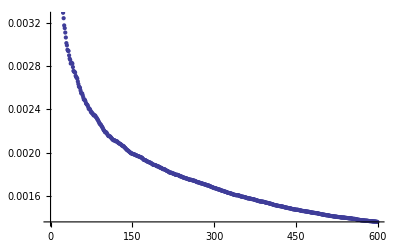

## leaf6dot2r2c2

running maxs

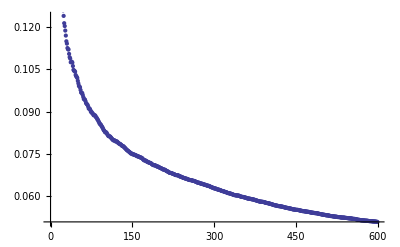

```mathematica
precision=500;
means={};
maxs={};
For[n=1,n<600,n++;
backorbit={};
fx=ls[[n,2]];
For[a=0,j=a<Length[list],a++;
If[list[[a,1]]==n,backorbit=Append[backorbit,list[[a,3]]]]];
means=Append[means,Sqrt[n/Log[n]]*Mean[relDevWOLogs[backorbit,fx,precision]]];
maxs=Append[maxs,Sqrt[n/Log[n]]*Max[relDevWOLogs[backorbit,fx,precision]]]
];
Print["means"];
Print[ListPlot[means]];
Print["maxs"];
Print[ListPlot[maxs]]
```

## leaf6dot2r1c1

means

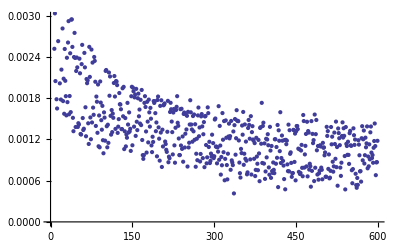

## leaf6dot2r1c2

maxs